```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### Range of densities

```mathematica
{triggermass[0.85],triggermass[1.37]}
```

{0.00337513,0.0000124363}

```mathematica
{Massreverse[0.85],Massreverse[1.25],Massreverse[1.37]}
```

{7.1606,8.46005,9.50943}

```mathematica
{Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->7.16},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->8.46},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->9.5}}
```

{(7.20147×10^29)/Centimeter^3,(1.43688×10^31)/Centimeter^3,(1.57551×10^32)/Centimeter^3}

```mathematica
6*{(7.201468136264897*^29)/Centimeter^3,(1.4368817984738546*^31)/Centimeter^3,(1.5755095624615844*^32)/Centimeter^3}
```

{(4.32088×10^30)/Centimeter^3,(8.62129×10^31)/Centimeter^3,(9.45306×10^32)/Centimeter^3}

```mathematica
Convert[9.453057374769507*^32 Centimeter^-3(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

7.56245 ElectronVolt^3 Mega^3

WD data

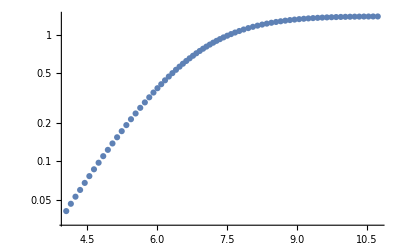

```mathematica
ListLogPlot[WD]
```

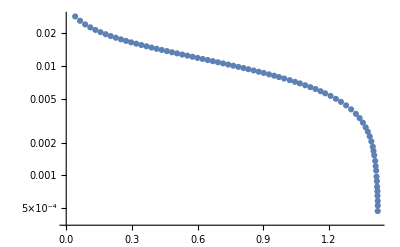

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.00230345 √(1/Radplot[1.25])

```mathematica
vesc[0.85]
```

0.0198191

```mathematica
Radplot[1.40]
```

0.00185935

```mathematica
vesc[1.42]
```

0.086269

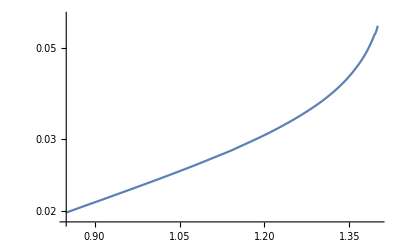

```mathematica
LogPlot[vesc[M],{M,0.85,1.4}]
```

#### λ_T as function of WD mass

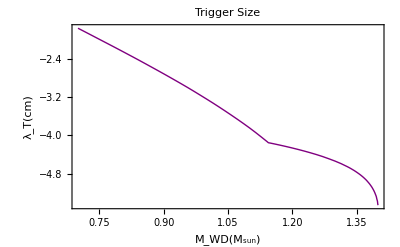

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
Plot[Log10[triggermass[M]],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### E_boom (GeV) as function of WD mass

```mathematica
10^logρ Convert[Gram/Centimeter^3 1/(12 Giga ElectronVolt/SpeedOfLight^2)*(200 Mega ElectronVolt Fermi)^3,(Mega ElectronVolt)^3]*(1/(Mega ElectronVolt))^3
```

3.73973×10^-10 10^logρ

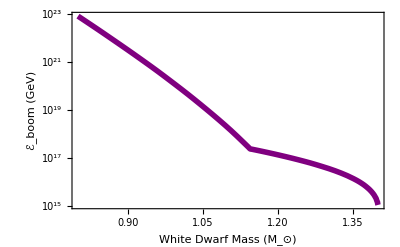

```mathematica
nionMeV[M_]:=Convert[10^Massreverse[M] Gram/Centimeter^3*SpeedOfLight^2/(12Giga ElectronVolt)*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]*1/(Mega ElectronVolt)^3
nionMeV2[logρ_]:=3.7397260789901873*^-10 10^logρ
eboom[M_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(triggermass[M](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV[M],Z->6})]
eboomdensity[logρ_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(trigger[10^logρ](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV2[logρ],Z->6})]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,None},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_⊙)","ℰ_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### How much of the WD detector should we observe?

```mathematica
restrict=1/2;
```

#### SN information

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
integralcollision[logmdm_]:=Re[NIntegrate[vesc[x]^3 (4π)/3(Radplot[x]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
integraldecay[logmdm_]:=Re[NIntegrate[vesc[1.25] (4π)/3(Radplot[1.25]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlessdecay=Convert[1/snrate (0.4(Giga ElectronVolt)/Centimeter^3)/(10^logmdm Giga ElectronVolt)(SpeedOfLight SolarRadius^3)/(10^-3 SpeedOfLight),Giga Year] 1/(Giga Year);
```

#### DM Wind - Collision Constraints

```mathematica
σcollision*(vesc/vth Rwd/Rsta)^-1
```

(6 mdm^2 Rsta v^2 vth Γcollision)/(π Rwd^4 vesc^4 ρdm^2)

```mathematica
Convert[σcollision*(vesc/vth Rwd/Rsta)^-1/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3,vth->Sqrt[10^-6/mdm],Rsta->},Centimeter^2] 1/Centimeter^2
```

Convert::incomp: Incompatible units in (1.75817×10^-43 10^(2 logmdm) Centimeter^6 Rsta Second^2 vth)/(Giga Meter^6 Year) and Centimeter^2.

(1.75817×10^-43 10^(2 logmdm) Centimeter^4 Rsta Second^2 vth)/(Giga Meter^6 Year)

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3(Rwd*restrict)^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

1.01577×10^-20

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

1.62523×10^-27

```mathematica
eboom[1.4]
```

15.0338

```mathematica
(Log10[unitlesscollision 1/integralcollision[15.04]]/.logmdm->15.04)
```

-16.6446

```mathematica
SNlist=Table[{logmdm,Log10[unitlesscollision 1/integralcollision[logmdm]]},{logmdm,15.04,24,0.1}];
```

```mathematica
SNcollision=Plot[Interpolation[SNlist][logmdm],{logmdm,15.04,24},PlotStyle->{Green,Thick}];
```

```mathematica
eboomlimitcollisionf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-35,-2}];
eboomlimitcollisionf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{-35,-2}];
collisionlimitSN=Plot[( 100 Sign[x-eboom[1.40]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.0065],Green}],PlotRange->{-16.104061761297505,5}];
RXcollision=Plot[Log10[σobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];
XLabelCollision={{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"},{18,"10^18"},{19,"10^19"},{20,"10^20"},{21,"10^21"},{22,"10^22"},{23,"10^23"},{24,"10^24"},{25,"10^25"}};
YLabelCollision={{-30,"10^-30"},{-25,"10^-25"},{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"}};
canvascollisionf1=Plot[-100,{logmdm,15,23},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-28,-7},Axes->None];
```

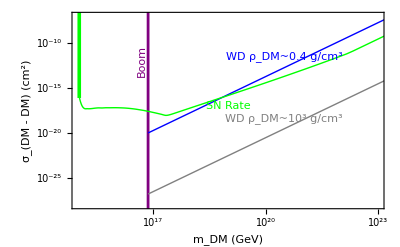

```mathematica
collisionobservation=Show[canvascollisionf1,eboomlimitcollisionf1,RXcollision,SNcollision, NuStarcollision,collisionlimitSN,Graphics[Inset[Style["WD ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{20.5,-11.5},{0,0},10,{1,1/2.1}]],Graphics[Inset[Style["WD ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{20.5,-18.4},{0,0},10,{1,1/2.1}]],Graphics[Inset[Style["SN Rate",Small,Green,FontFamily->"Helvetica"],{19,-17},{0,0},10,{1,1/3}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{16.7,-12},{0,0},10,{0,1}]]]
```

#### DM Wind - Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3(Rwd restrict)^3;
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

3.15562×10^11

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

7.88906×10^14

```mathematica
Log10[unitlessdecay integraldecay[15.04]]/.logmdm->15.04
```

4.06248

```mathematica
SNlistdecay=Table[{logmdm,Log10[unitlessdecay integraldecay[logmdm]]},{logmdm,15.04,24,0.1}];
```

```mathematica
SNdecay=Plot[Interpolation[SNlistdecay][logmdm],{logmdm,15.04,24},PlotStyle->{Green,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];eboomlimitdecayf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{3.5,20}];
eboomlimitdecayf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{3.5,20}];
decaylimitSN=Plot[(100 Sign[x-eboom[1.4]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.006],Green}],PlotRange->{-10,4.062484865023983}];
YLabelDecay={{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}};
canvasdecayf1=Plot[-100,{logmdm,15,23},Frame->True,FrameTicks->{{YLabelDecay,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{3.5,15},Axes->None];
```

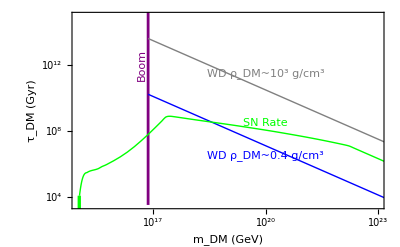

```mathematica
decayobservation=Show[canvasdecayf1,eboomlimitdecayf1,RXdecay,NuStardecay,SNdecay,decaylimitSN,Graphics[Inset[Style["WD ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{20,6.5},{0,0},10,{1,-1/2.3}]],Graphics[Inset[Style["WD ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{20,11.5},{0,0},10,{1,-1/2.3}]],Graphics[Inset[Style["SN Rate",Small,Green,FontFamily->"Helvetica"],{20,8.5},{0,0},10,{1,-1/10}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{16.7,12},{0,0},10,{0,1}]]]
```

#### DM Capture - Constraints

```mathematica
nionMeV[1.25] MeV^3*(200 MeV 10^-13 cm)^-3
```

(1.34833×10^31)/cm^3

```mathematica
Rth=FullSimplify[((T Mpl^2)/(mdm (nion mc)))^(1/2)*0.2GeV 10^-15 m/.{T->10^-6 GeV,Mpl->10^19 GeV,mdm->GeV 10^logmdm,nion->nionMeV[1.25] MeV^3(GeV/(10^3 MeV))^3,mc->12GeV},GeV>0]*1/m;
```

```mathematica
Rth/.logmdm->16
```

0.0005559

```mathematica
tcollapse=Convert[4 Pi/3(nion mc)(Rth Meter)^3 *(ρdm π Rwd^2 vesc^2/v)^-1 *(200 Mega ElectronVolt*Fermi)^-3/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3,nion->nionMeV[1.25](Mega ElectronVolt)^3,mc->12 Giga ElectronVolt},Second] 1/Second;
```

```mathematica
tcollapse/.logmdm->16
```

25.1432

```mathematica
tsink=Convert[(Radplot[1.25]SolarRadius)/(Sqrt[10^-6/10^logmdm]SpeedOfLight),Second]*1/Second;
```

```mathematica
tsink/.logmdm->16
```

1.11026×10^9

```mathematica
twind=Convert[(Radplot[1.25]SolarRadius)/(vesc[1.25]SpeedOfLight),Second]*1/Second
```

0.333324

```mathematica
σcollapse=Log10[FullSimplify[(Rsta^2/Ndm^2)*(0.2GeV 10^-13 cm)^2/.{Ndm->(ρwd (T Mpl^2/(ρwd mdm))^(3/2)1/mdm),Rsta->ρwd (T Mpl^2/(ρwd mdm))^(3/2)1/Mpl^2}/.{mdm->GeV 10^logmdm,v->10^-3,ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,vesc->vesc[1.25],ρwd->nionMeV[1.25] MeV^3 12GeV (GeV/(10^3 MeV))^3,Mpl->10^19 GeV,τ->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->restrict Radplot[1.25]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV},GeV>0] 1/cm^2];
```

```mathematica
σinfall=Log10[FullSimplify[((ρdm/mdm Rwd^2 vesc^2/v)^2 τ/Sqrt[T/mdm] 1/Rsta)^-1(0.2GeV 10^-13 cm)^2/.Rsta->ρwd (T Mpl^2/(ρwd mdm))^(3/2)1/Mpl^2/.{mdm->GeV 10^logmdm,v->10^-3,ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,vesc->vesc[1.25],ρwd->nionMeV[1.25] MeV^3 12GeV (GeV/(10^3 MeV))^3,Mpl->10^19 GeV,τ->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->restrict Radplot[1.25]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV},GeV>0] 1/cm^2];
```

```mathematica
τinfall=Log10[FullSimplify[Convert[τdm (vesc/(Sqrt[T/mdm]SpeedOfLight))/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3,T->10^-6 Giga ElectronVolt},Giga Year] 1/(Giga Year)]];
```

```mathematica
Schcollapse=Plot[σcollapse,{logmdm,eboom[1.25],32},PlotStyle->{Red,Thick}];
Schinfall=Plot[σinfall,{logmdm,eboom[1.25],32},PlotStyle->{Black,Thick}];
decayinfall=Plot[τinfall,{logmdm,eboom[1.25],32},PlotStyle->{Black,Thick}];
```

#### Transit Constraints, ϵ (in MeV!) released per collision

```mathematica
transitboom[M_]:=(((10^eboom[M] 10^3)MeV)/(nionMeV[M] MeV^3(triggermass[M]cm*(200 MeV*10^-13 cm)^-1))1/(ϵ MeV)(200 MeV *10^-13 cm)^2)1/cm^2;
```

```mathematica
transitreverse=Interpolation[Table[{Log10[transitboom[M]],M}/.{ϵ->10^6},{M,0.4,1.4,0.01}],InterpolationOrder->1];
integraltransit[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]),1.40}]]
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
unitlesstransit=Convert[1/snrate*0.4 (Giga ElectronVolt)/Centimeter^3*SpeedOfLight^2/(10^-3 SpeedOfLight)*SolarRadius^2,Giga ElectronVolt] 1/(Giga ElectronVolt);
```

```mathematica
transitRX=Log10[Convert[ρdm π (restrict Rwd)^2(vesc/v)^2 v τwd/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4(Giga ElectronVolt)/Centimeter^3,τwd->5 Giga Year},Giga ElectronVolt] 1/(Giga ElectronVolt)]
```

44.2614

```mathematica
transitNuStar=Log10[Convert[ρdm π (restrict Rwd)^2(vesc/v)^2 v τwd/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3(Giga ElectronVolt)/Centimeter^3,τwd->5 Giga Year},Giga ElectronVolt] 1/(Giga ElectronVolt)]
```

47.6593

```mathematica
Log10[transitboom[1.40]]/.ϵ->10^6
```

-15.7731

```mathematica
Log10[transitboom[0.85]]/.ϵ->10^6
```

-8.13791

```mathematica
SNtransitlineTeV=Log10[unitlesstransit integraltransit[Log10[transitboom[0.85]]/.ϵ->10^6]];
SNtransitlineTeVflat=Log10[unitlesstransit integraltransit[Log10[transitboom[1.3999]]/.ϵ->10^6]];
```

```mathematica
transitSN=Interpolation[Table[{Log10[unitlesstransit integraltransit[logσ]],logσ},{logσ,Log10[transitboom[1.3999]]/.ϵ->10^6,Log10[transitboom[0.85]]/.ϵ->10^6,0.01}]];
```

#### Model-dependent crust stopping calculation (R_crust~ 50 km, ρ_crust~ 10^-2 ρ_central)

```mathematica
crust=Log10[Convert[(10^logmdm Giga ElectronVolt vesc[1.25]^2)/(50Kilo Meter 10^-2 nionMeV[1.25](Mega ElectronVolt)^3(200 Mega ElectronVolt Fermi)^-3)1/(ϵ Mega ElectronVolt),Centimeter^2] 1/Centimeter^2];
```

```mathematica
crustplotTeV=Plot[crust/.ϵ->10^6,{logmdm,20,55},PlotStyle->{Dashed,Black,Thick}];
photontransitTeV=Plot[Log10[transitboom[1.25]]/.ϵ->10^6,{logmdm,24,52},PlotStyle->{Thick,Purple}];
transitSNTeV=Plot[transitSN[logmdm],{logmdm,Log10[unitlesstransit integraltransit[Log10[transitboom[1.3999]]/.ϵ->10^6]],Log10[unitlesstransit integraltransit[Log10[transitboom[0.85]]/.ϵ->10^6]]},PlotStyle->{Green,Thick}];
fluxlimitRX=Plot[( 100 Sign[logmdm-transitRX]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.005],Blue}],PlotRange->{-20,10}];
fluxlimitNuStar=Plot[( 100 Sign[logmdm-transitNuStar]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.005],Gray}],PlotRange->{-20,10}];
fluxlimitSN=Plot[(100 Sign[logmdm-SNtransitlineTeV]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.0069],Green}],PlotRange->{Log10[transitboom[0.85]]/.ϵ->10^6,10}];
tailSN=Plot[Log10[transitboom[1.3999]/.ϵ->10^6],{logmdm,24,SNtransitlineTeVflat},PlotStyle->{Green,Thick}];
YLabelTransit={{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"},{5,"10^5"}};
XLabelTransit={{25,"10^25"},{30,"10^30"},{35,"10^35"},{40,"10^40"},{45,"10^45"},{50,"10^50"}};
canvastransit=Plot[-100,{x,27,50},Frame->True,FrameTicks->{{YLabelTransit,None},{XLabelTransit,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(photon, TeV) (cm^2)"},PlotRange->{-18,3},Axes->None];
```

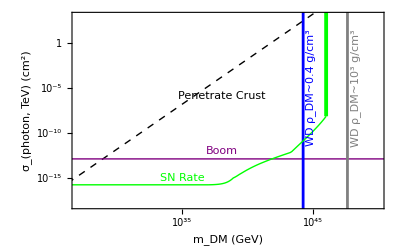

```mathematica
transitobservation=Show[canvastransit,crustplotTeV,photontransitTeV,fluxlimitRX,fluxlimitNuStar,fluxlimitSN,tailSN,transitSNTeV,Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{38,-12},{0,0},4,{1,0}]],
Graphics[Inset[Style["SN Rate",Small,Green,FontFamily->"Helvetica"],{35,-15},{0,0},4,{1,0}]],Graphics[Inset[Style["WD ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{48.3,-5},{0,0},12,{0,1}]],Graphics[Inset[Style["WD ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{44.8,-5},{0,0},12,{0,1}]],Graphics[Inset[Style["Penetrate Crust",Small,FontFamily->"Helvetica"],{38,-5.9},{0,0},10,{1,3/5}]]]
```

#### Competing constraints: deplete galactic halo by O(1), CMB polarization, terrestrial cosmic ray experiments, general DM decay.

```mathematica
σHalo=Convert[Barn/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCMB=Convert[Convert[3 10^-26 Centimeter^3/Second*1/(100 Giga ElectronVolt) (((10 ElectronVolt)/(mdm Giga ElectronVolt))^(1/2)SpeedOfLight)^-1,Barn/(Giga ElectronVolt)]mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCR=Convert[1/(5Year)*(((0.3 Giga ElectronVolt)/Centimeter^3 1/(mdm Giga ElectronVolt))^2 10^-3 SpeedOfLight*(50 Kilo Meter)^2(50 Kilo Parsec))^-1,Centimeter^2] 1/Centimeter^2/.mdm->10^logmdm;
τCR=Convert[(0.3 Giga ElectronVolt)/Centimeter^3*1/(mdm Giga ElectronVolt)*(50 Kilo Meter)^2(50 Kilo Parsec)*5Year,Giga Year] 1/(Giga Year)/.mdm->10^logmdm;
τcosmo=10^2 Giga Year*1/(Giga Year);
```

#### Plotting competing constraints

```mathematica
σHaloplot=Plot[Log10[σHalo],{logmdm,eboom[1.25],35},PlotStyle->{Magenta,Thick}];
σCMBplot=Plot[Log10[σCMB],{logmdm,eboom[1.25],35},PlotStyle->{Green,Thick}];
σCRplot=Plot[Log10[σCR],{logmdm,eboom[1.25],35},PlotStyle->{Red,Thick}];
τCRplot=Plot[Log10[τCR],{logmdm,eboom[1.25],35},PlotStyle->{Cyan,Thick}];
```

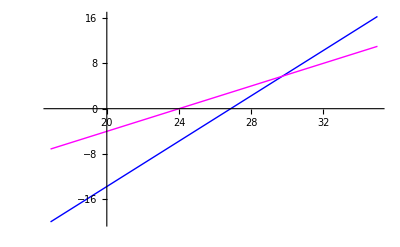

```mathematica
Show[RXcollision,σHaloplot]
```

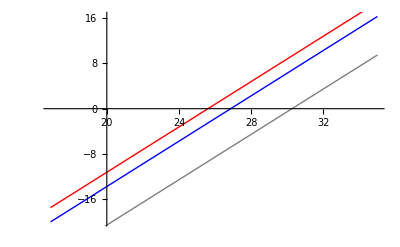

```mathematica
Show[RXcollision,NuStarcollision,σCRplot]
```

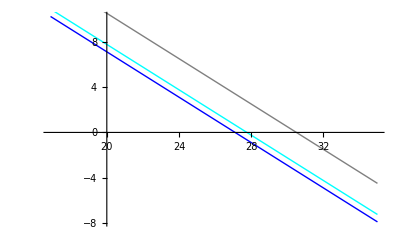

```mathematica
Show[RXdecay,NuStardecay,τCRplot]
```

#### Q-ball boom σ_Q

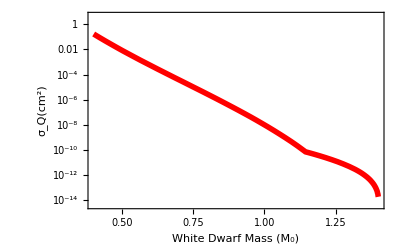

```mathematica
LogPlot[transitboom[M]/.ϵ->10^4,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### SUSY Q-ball constraints, m_s=10^3 Gev

```mathematica
Log10[(1/π 10^-12 cm^2)^2(0.2 GeV 10^-13 cm)^-4(10^3 GeV)^4]
```

41.8016

```mathematica
(10^3 GeV)((1/π 10^-12 cm^2)^2(0.2 GeV 10^-13 cm)^-4(10^3 GeV)^4)^(3/4)
```

2.24484×10^34 GeV

```mathematica
Log10[((10^transitNuStar GeV)/(10^3 GeV))^(4/3)]
```

59.5457

```mathematica
Log10[((10^19 GeV)/(10^3 GeV))^4]
```

64